```mathematica
(*Initialize*)
eigs={};
neig=Length[eigs];
```

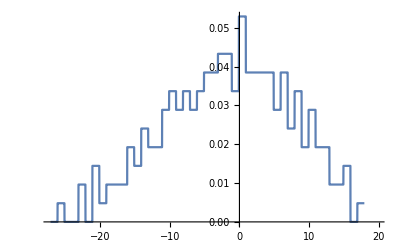

```mathematica
(*Density of State*)
bin=1.;
eMin=Min[eigs];
eMax=Max[eigs];
dELis=Array[eMin+bin*#&,{Floor[(eMax-eMin)/bin]}];
rhoLis={};
Do[AppendTo[rhoLis,Length[Select[eigs,dELis[[i]]≤#≤dELis[[i+1]]&]]],{i,1,Length[dELis]-1}];
rhoLis=rhoLis/(Total[rhoLis*bin]);
rho[x_]:=rhoLis[[Floor[(x-eMin)/bin]+1]];
Plot[rho[x],{x,eMin,eMax}]
```

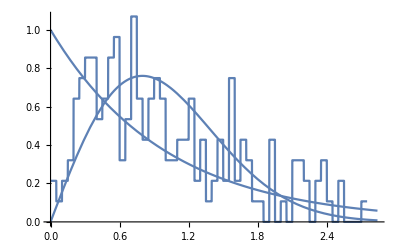

```mathematica
(*Normalized Spacing*)
grp=4;
per=0.1*neig;
half=Floor[per/2];
spc={};
Do[Clear[avg];avg=(eigs[[half+grp j]]-eigs[[half+grp(j-1)]])/grp;
Do[AppendTo[spc,(eigs[[half+i]]-eigs[[half+i-1]])/avg];,{i,1+grp(j-1),grp j }];
,{j,1,Floor[(neig-per)/grp]}
];
bin=0.05;
spcM=Max[spc];
dELis=Array[bin*(#-1)&,{Floor[spcM/bin]}];
spcLis={};
Do[AppendTo[spcLis,Length[Select[spc,dELis[[i]]≤#≤dELis[[i+1]]&]]],{i,1,Length[dELis]-1}];
spcLis=spcLis/(Total[spcLis*bin]);
spcFunc[x_]:=spcLis[[Floor[(x)/bin]+1]];
Plot[spcFunc[x],{x,0.,spcM}]~Show~Plot[(π s)/2. Exp[(-π s^2)/4.],{s,0.,spcM},PlotRange->{0.,1.}]~Show~Plot[Exp[-s],{s,0.,spcM},PlotRange->{0.,1.}]
```